```mathematica
(* orbital-like functions: f(x,y,z)=A*g(r)*h(x,y,z),r=√(x^2+y^2+z^2)
1s g(r)=ⅇ^-r, h(x,y,z)=1
2 Subscript[p, z] g(r)=ⅇ^(-r/2), h(x,y,z)=z
3 Subscript[d, z^2] g(r)=ⅇ^(-r/3), h(x,y,z)=3 z^2-r^2 *)
```

```mathematica
r[x_,y_,z_]:=√(x^2+y^2+z^2)
```

```mathematica
f[x_,y_,z_]:=ⅇ^(-r[x,y,z]);
ContourPlot3D[f[x,y,z]==0.1,{x,-3,3},{y,-3,3},{z,-3,3}](* 注意“==” *)
```

-Graphics3D-

```mathematica
f2[x_,y_,z_]:=ⅇ^(-r[x,y,z]/2) z;
ContourPlot3D[{f2[x,y,z]==0.1,f2[x,y,z]==-0.1},{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
f2[x_,y_,z_]:=ⅇ^(-r[x,y,z]/2) z;
ContourPlot3D[{f2[x,y,z]==0.1,f2[x,y,z]==-0.1},{x,-10,10},{y,-10,10},{z,-10,10},Mesh->None,ContourStyle->{{Green,Specularity[White,50]},{Yellow,Specularity[White,50]}}]
```

-Graphics3D-

```mathematica
f2[x_,y_,z_]:=ⅇ^(-r[x,y,z]/2) z;
ContourPlot3D[{f2[x,y,z]==0.1,f2[x,y,z]==-0.1},{x,-10,10},{y,-10,10},{z,-10,10},Mesh->None,ContourStyle->{{Green,Specularity[White,100]},{Yellow,Specularity[White,100]}}]
```

-Graphics3D-

```mathematica
f3[x_,y_,z_]:=ⅇ^(-r[x,y,z]/3) (3 z^2-r[x,y,z]^2);
ContourPlot3D[{f3[x,y,z]==0.1,f2[x,y,z]==-0.1},{x,-30,30},{y,-30,30},{z,-30,30},Mesh->None,ContourStyle->{{Green,Specularity[White,10]},{Yellow,Specularity[White,10]}}]
```

-Graphics3D-

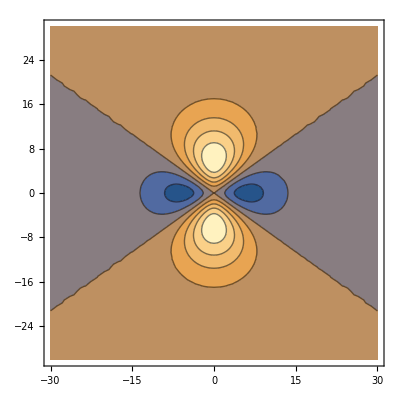

```mathematica
r[x_,z_]:=Sqrt[x^2+z^2];
f4[x_,z_]:=ⅇ^(-r[x,z]/3) (3 z^2-r[x,z]^2);
ContourPlot[f4[x,z],{x,-30,30},{z,-30,30},PlotRange->All](* x-z平面截面图 *)
```

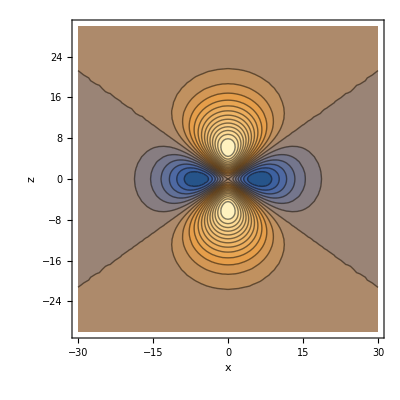

```mathematica
r[x_,z_]:=Sqrt[x^2+z^2];
f4[x_,z_]:=ⅇ^(-r[x,z]/3) (3 z^2-r[x,z]^2);
ContourPlot[f4[x,z],{x,-30,30},{z,-30,30},FrameLabel->{"x","z"},Contours->20,PlotRange->All](* x-z平面截面图 *)
```

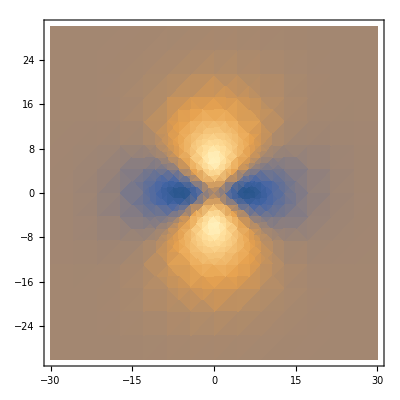

```mathematica
r[x_,z_]:=Sqrt[x^2+z^2];
f4[x_,z_]:=ⅇ^(-r[x,z]/3) (3 z^2-r[x,z]^2);
DensityPlot[f4[x,z],{x,-30,30},{z,-30,30},PlotRange->All]
```